```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/"];
```

```mathematica
datafull=Import["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/data/ccm1_data.csv",HeaderLines->1];
```

```mathematica
Get["SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
data=Table[Take[datafull,UpTo@i],{i,Ceiling@Range[45920.3,459203,45920.3]}];
```

fixed step size

```mathematica
(* thickness=networkdatabinned[6,0.01];
width=networkdatabinned[5,20]; *)
```

```mathematica
feature=9;
datadimension=10;
rawaim=Table[Symbol["data"][[i]][[All,feature]],{i,Range@datadimension}];
aim=Table[DeleteCases[i,"NA"],{i,rawaim}];
campaign=Table[Delete[Symbol["data"][[i[[1]]]][[All,2]],Position[i[[2]],"NA"]],
{i,MapThread[{#1,#2}&,{Range@datadimension,rawaim}]}];
seri=Table[Delete[Symbol["data"][[i[[1]]]][[All,1]],Position[i[[2]],"NA"]],
{i,MapThread[{#1,#2}&,{Range@datadimension,rawaim}]}];
```

```mathematica
min=Table[Min[Sort[DeleteDuplicates[i]],0.1],{i,aim}]
```

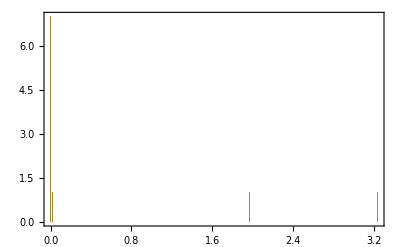

```mathematica
Histogram[data[[All,9]],{10^6},Frame->True,PlotRange->All]
```

```mathematica
max=Table[Ceiling[Max[Sort[DeleteDuplicates[i]]]]+step,{i,aim}];
```

```mathematica
binningamount=Table[Length[DeleteCases[BinLists[i[[1]],{i[[2]],i[[3]],step}],{}]],
{i,MapThread[{#1,#2,#3}&,{aim,min,max}]}];
binning=Table[Table[Catch[Do[If[IntervalMemberQ[Interval[i],(k[[1]])[[j]]]==True,Throw[i]],
{i,Partition[Range[k[[2]],k[[3]],step],2,1]}]],{j,Length[k[[1]]]}],{k,MapThread[{#1,#2,#3}&,
{aim,min,max}]}];
aim=Table[DeleteCases[i,Null],{i,binning}];
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[5,20,10];]
```

{583.668,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,600,Green],{i,Range@10}];
```

```mathematica
VertexDegree@graphsandnodenumbers[[All,1]][[1]]
```

{2,6,6,4,13,11,13,13,15,10,12,17,15,16,19,25,24,17,17,23,18,20,22,22,22,22,23,21,24,24,21,20,23,21,26,21,20,20,23,19,14,21,15,14,15,11,13,13,9,3}

```mathematica
correlationfunction[network_,choice_]:=Module[{De,CC,BC,DeBC,CCBC,out},
De=VertexDegree[network];
CC=LocalClusteringCoefficient[network];
BC=BetweennessCentrality[network];
DeBC=Which[choice==1,SpearmanRho[De,BC],choice==2,Correlation[De,BC],choice==3,KendallTau[[De,BC]]];
CCBC=Which[choice==1,SpearmanRho[CC,BC],choice==2,Correlation[CC,BC],choice==3,KendallTau[[CC,BC]]];
out={DeBC,CCBC}];
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.772747,-0.886977},{0.806642,-0.925971},{0.871641,-0.948685},{0.758372,-0.967046},{0.820209,-0.908165},{0.72343,-0.915982},{0.744424,-0.903253},{0.69551,-0.891272},{0.694933,-0.891884},{0.707359,-0.925486}}

{{0.650184,-0.797802},{0.645857,-0.816833},{0.736749,-0.870549},{0.638188,-0.871099},{0.605696,-0.754086},{0.575146,-0.724827},{0.565383,-0.713916},{0.586362,-0.708922},{0.571063,-0.69297},{0.576735,-0.742365}}

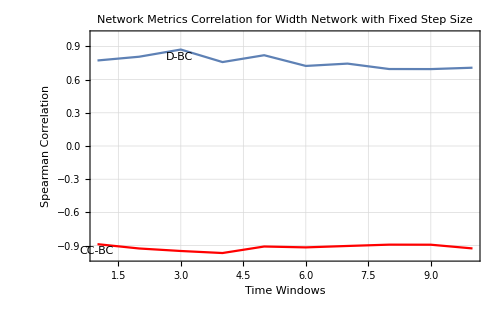
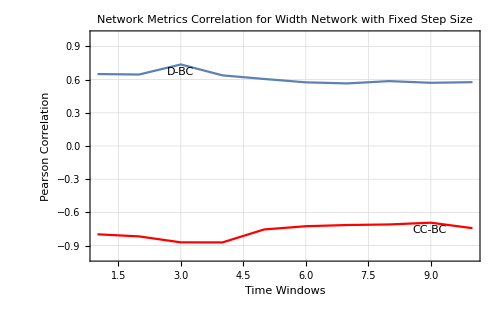

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"]}
```

```mathematica
randomnessfunction[network_,choice_]:=Module[{randomgraphs,MuDeBC,MuCCBC,XDeBC,XCCBC,SigmaDeBC,SigmaCCBC,ZDeBC,ZCCBC,final},SeedRandom[17];randomgraphs=RandomGraph[{VertexCount[network],EdgeCount[network]},1000];MuDeBC = Mean[Table[correlationfunction[randomgraphs[[i]],choice][[1]],{i,1000}]];MuCCBC = Mean[Table[correlationfunction[randomgraphs[[i]],choice][[2]],{i,1000}]];XDeBC= correlationfunction[network,choice][[1]];XCCBC= correlationfunction[network,choice][[2]];
SigmaDeBC =StandardDeviation[Table[correlationfunction[randomgraphs[[i]],choice][[1]],{i,1000}]];SigmaCCBC =StandardDeviation[Table[correlationfunction[randomgraphs[[i]],choice][[2]],{i,1000}]];ZDeBC=(XDeBC-MuDeBC)/SigmaDeBC;ZCCBC=(XCCBC-MuCCBC)/SigmaCCBC;final={ZDeBC,ZCCBC}];
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-9.4506},{2,-9.30001},{3,-5.58362},{4,-13.3269},{5,-10.0046},{6,-16.8935},{7,-14.6377},{8,-18.5627},{9,-20.2898},{10,-17.6157}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-4.01429},{2,-4.06799},{3,-4.45495},{4,-4.35626},{5,-4.1688},{6,-4.17113},{7,-4.03569},{8,-4.16757},{9,-4.12816},{10,-4.46511}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-18.7431},{2,-24.4982},{3,-18.466},{4,-26.6219},{5,-32.1904},{6,-34.9351},{7,-34.7989},{8,-33.6571},{9,-36.2215},{10,-34.865}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-3.49246},{2,-3.38845},{3,-3.99782},{4,-3.83444},{5,-3.14652},{6,-2.94854},{7,-2.80578},{8,-3.00882},{9,-2.80236},{10,-3.24896}}

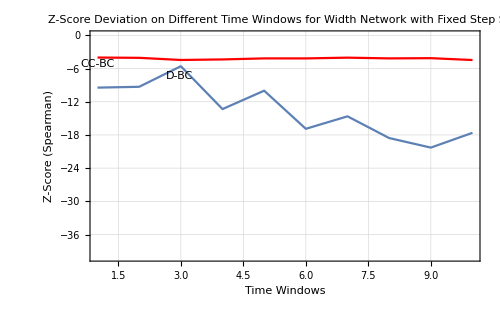
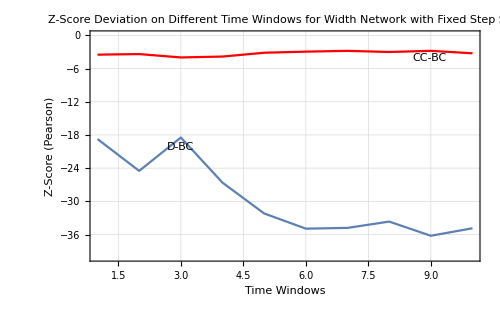

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-40,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"]}
```